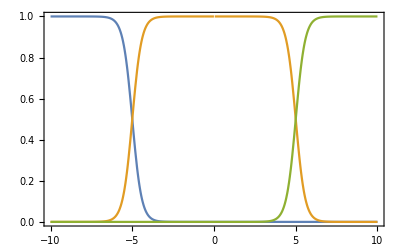

```mathematica
xmale[x_]:=1/(1+Exp[3.5 (x+5)]);
xstredni[x_]:=Min[1/(1+Exp[-3.5 (x+5)]),1/(1+Exp[3.5 (x-5)])];
xvelke[x_]:=1/(1+Exp[-3.5 (x-5)]);
Plot[{xmale[x],xstredni[x],xvelke[x]}, {x, -10, 10}, 
Frame->{True, True, False, False}, 
Axes-> False,
PlotRange->{{-10,10}, {0,1}}]
```

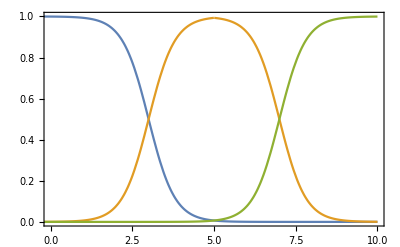

```mathematica
ymale[x_]:=1/(1+Exp[2.5 (x-3)]);
 ystredni[x_]:=Min[1/(1+Exp[-2.5 (x-3)]),1/(1+Exp[2.5 (x-7)])];
 yvelke[x_]:=1/(1+Exp[-2.5 (x-7)]);
Plot[{ymale[x],ystredni[x],yvelke[x]}, {x, -10, 10}, 
Frame->{True, True, False, False}, 
Axes-> False,
PlotRange->{{0,10}, {0,1}}]
```

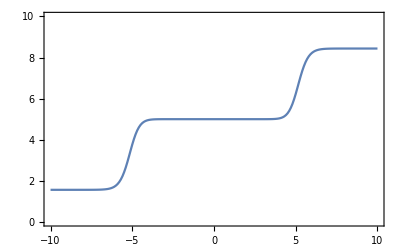

```mathematica
z={};
For[x=-10,x≤10,x+=0.1,
total=0;
totalp=0;
For[y=0,y≤10,y+=0.1,
temp=Max[Min[xmale[x],ymale[y]],
		Min[xstredni[x],ystredni[y]],
		Min[xvelke[x],yvelke[y]]];
total+=temp*y;
totalp+=temp;
];
z=Append[z,{x,total/totalp}]
];
ListLinePlot[z,Frame->{True,True,False,False},Axes->False,PlotRange->{{-10,10},{0,10}}]
```